I use x̄=omega x as variable x here. In other words, the x I am going to use is in fact omega x.

```mathematica
imgsize=Large;
imgpadding={{70, 20}, {50, 10}};
```

```mathematica
beta=0.1
alpha=0.1
sin2thetav=0.917
cos2thetav=0.4
```

0.1

0.1

0.917

0.4

```mathematica
eqnc2 = -c2''[x]+(-I alpha Cos[beta x] cos2thetav+( -beta Tan[beta x] + I ))c2'[x]+(I/2 alpha Cos[beta x] cos2thetav(-beta Tan[beta x]+I)+(alpha)^2/4 Cos[beta x]^2(cos2thetav^2-sin2thetav^2))c2[x]==0
```

c2[x] (-0.00170222 Cos[0.1 x]^2+(0.+0.02 ⅈ) Cos[0.1 x] (ⅈ-0.1 Tan[0.1 x]))+(ⅈ-(0.+0.04 ⅈ) Cos[0.1 x]-0.1 Tan[0.1 x]) c2'[x]-c2''[x]==0

```mathematica
endpoint=70
```

70

```mathematica
solc2=NDSolve[{eqnc2,c2[0]==0,c2'[0]==-I/2 alpha sin2thetav},c2,{x,0,endpoint}]
```

{{c2→InterpolatingFunction[{{0., 70.}}, <>]}}

```mathematica
c2Fun=First[c2/.solc2]
```

InterpolatingFunction[{{0., 70.}}, <>]

```mathematica
eqnc1=I D[c1[x],x]==alpha cos2thetav c1[x]Cos[beta x]/2+alpha sin2thetav Cos[beta x]c2Fun[x]Exp[-I alpha x]/2
solc1=NDSolve[{eqnc1,c1[0]==1},c1,{x,0,endpoint}]
```

ⅈ c1'[x]==0.02 c1[x] Cos[0.1 x]+0.04585 ⅇ^((0.-0.1 ⅈ) x) Cos[0.1 x] InterpolatingFunction[{{0., 70.}}, <>][x]

{{c1→InterpolatingFunction[{{0., 70.}}, <>]}}

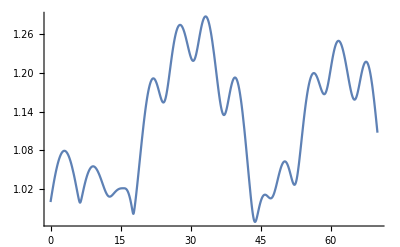

```mathematica
rwaNorm=Plot[Evaluate[Abs[c1[x]]^2+Abs[c2Fun[x]]/.solc1[[1]]],{x,0,endpoint},PlotRange->All]
```

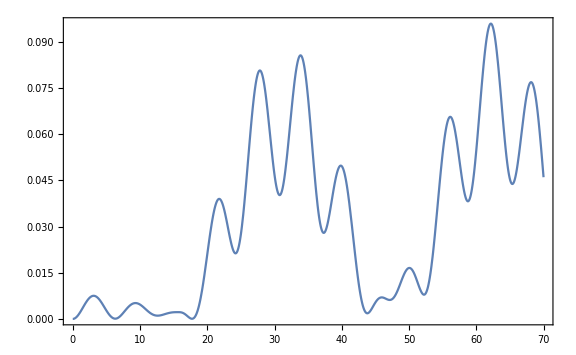

```mathematica
rwaP=Plot[Evaluate[Abs[c2Fun[x]]^2/(Abs[c1[x]]^2+Abs[c2Fun[x]]/.solc1[[1]])/.solc1[[1]]],{x,0,endpoint},PlotRange->All,ImageSize->imgsize,Frame->True]
```

```mathematica
Manipulate[Plot[Evaluate[Abs[c2Fun[x]]^2/(Abs[c1[x]]^2+Abs[c2Fun[x]]/.solc1[[1]])/.solc1[[1]]],{x,0,end},PlotRange->All,ImageSize->imgsize,Frame->True],{end,10,endpoint}]
```

### Equation Set

```mathematica
eqnset=I c1'[x]==alpha cos2thetav c1[x]Cos[beta x]/2+alpha Cos[beta x] sin2thetav c2[x]Exp[-I x]/2&&I c2'[x]==alpha Cos[beta x] cos2thetav c2[x]/2+alpha Cos[beta x] sin2thetav c1[x] Exp[I x]/2
```

ⅈ c1'[x]==0.02 c1[x] Cos[0.1 x]+0.04585 ⅇ^(-ⅈ x) c2[x] Cos[0.1 x]&&ⅈ c2'[x]==0.04585 ⅇ^(ⅈ x) c1[x] Cos[0.1 x]+0.02 c2[x] Cos[0.1 x]

```mathematica
solset=NDSolve[{eqnset,c1[0]==1,c2[0]==0},{c1,c2},{x,0,30}]
```

{{c1→InterpolatingFunction[{{0., 30.}}, <>],c2→InterpolatingFunction[{{0., 30.}}, <>]}}

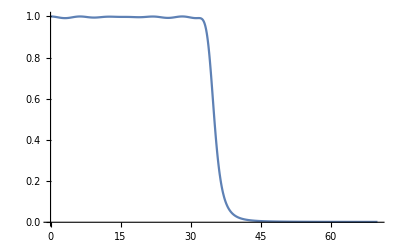

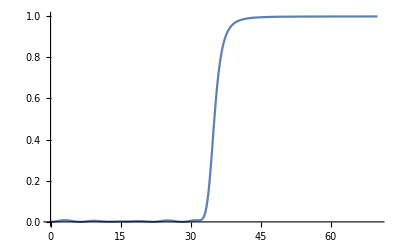

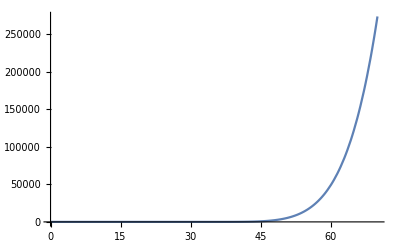

```mathematica
Plot[Evaluate[Abs[c1[x]]^2/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solset],{x,0,endpoint},PlotRange->All]
Plot[Evaluate[Conjugate[c2[x]]c2[x]/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solset],{x,0,endpoint},PlotRange->All]
Plot[Evaluate[(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solset],{x,0,endpoint},PlotRange->All]
```

```mathematica
Manipulate[Grid[{{Plot[Evaluate[Abs[c1[x]]^2/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solset],{x,0,end},PlotRange->All,ImageSize->imgsize,Frame->True,PlotLabel->"C_1",FrameLabel->{"ω x","|C_1|^2"},ImagePadding->imgpadding],
Plot[Evaluate[Conjugate[c2[x]]c2[x]/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solset],{x,0,end},PlotRange->All,ImageSize->imgsize,Frame->True,PlotLabel->"C_2",FrameLabel->{"ω x","|C_2|^2"},ImagePadding->imgpadding]},
{Plot[Evaluate[(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solset],{x,0,end},PlotRange->All,ImageSize->imgsize,Frame->True,PlotLabel->"Normalization",FrameLabel->{"ω x","|C_1|^2+|C_2|^2"},ImagePadding->imgpadding],Plot[{Evaluate[Abs[c1[x]]^2/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solset],Evaluate[Conjugate[c2[x]]c2[x]/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solset]},{x,0,end},PlotRange->All,ImageSize->imgsize,Frame->True,PlotLabel->"Merged",FrameLabel->{"ω x","|C_1|^2 and |C_2|^2"},ImagePadding->imgpadding]}}],{{end,endpoint,"Range"},10,endpoint,1}]
```

### RWA + SLOW Matter Frequency

```mathematica
omegaHatR[alp_,bet_,x_]=Sqrt[(1-bet-alp cos2thetav Cos[bet x]/2)^2+(alp sin2thetav /2)^2];
probability[alp_,bet_,x_]=alp^2 sin2thetav Sin[omegaHatR[alp,bet,x] x/2]^2/(2omegaHatR[alp,bet,x]^2)
```

(0.4585 alp^2 Sin[1/2 x √(0.210222 alp^2+(1-bet-0.2 alp Cos[bet x])^2)]^2)/(0.210222 alp^2+(1-bet-0.2 alp Cos[bet x])^2)

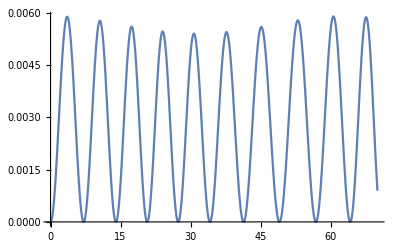

```mathematica
Plot[probability[alpha,beta,x],{x,0,endpoint}]
```

### Compare the two

```mathematica
Manipulate[Grid[{{Plot[Evaluate[Abs[c2Fun[x]]^2/(Abs[c1[x]]^2+Abs[c2Fun[x]]/.solc1[[1]])/.solc1[[1]]],{x,0,end},PlotRange->All,ImageSize->imgsize,Frame->True,PlotLabel->"RWA C_2",FrameLabel->{"ω x","|C_2|^2"},ImagePadding->imgpadding],Plot[Evaluate[Conjugate[c2[x]]c2[x]/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solset],{x,0,end},PlotRange->All,ImageSize->imgsize,Frame->True,PlotLabel->"Complete C_2",FrameLabel->{"ω x","|C_2|^2"},ImagePadding->imgpadding]},{Plot[{Evaluate[Abs[c2Fun[x]]^2/(Abs[c1[x]]^2+Abs[c2Fun[x]]/.solc1[[1]])/.solc1[[1]]],Evaluate[Conjugate[c2[x]]c2[x]/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solset]},{x,0,end},PlotRange->All,ImageSize->imgsize,Frame->True,PlotLabel->"RWA & Complete C_2",FrameLabel->{"ω x","|C_2|^2"},ImagePadding->imgpadding],Plot[{probability[alpha,beta,x],Evaluate[Conjugate[c2[x]]c2[x]/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solset]},{x,0,end},PlotRange->All,ImageSize->imgsize,Frame->True,PlotLabel->"Analytical & Complete C_2",FrameLabel->{"ω x","|C_2|^2"},ImagePadding->imgpadding]}}],{end,10,endpoint}]
```